```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Dir = "/home/matt/git/source/fast-fourier-transform/fast-fourier/results";
Thread1=Import[StringJoin[Dir,"/1.txt"], "Table"];
Thread2=Import[StringJoin[Dir,"/4.txt"], "Table"];
Thread3=Import[StringJoin[Dir,"/16.txt"], "Table"];
Thread4=Import[StringJoin[Dir,"/64.txt"], "Table"];
Thread5=Import[StringJoin[Dir,"/256.txt"], "Table"];
Thread6=Import[StringJoin[Dir,"/1024.txt"], "Table"];
```

```mathematica
DS1 = Table[{{Thread1[[n]][[1]],Thread1[[n]][[2]]},  ErrorBar[ Thread1[[n]][[3]] ]},{n,1,Length[Thread1]}];
DS2 = Table[{{Thread2[[n]][[1]],Thread2[[n]][[2]]},  ErrorBar[ Thread2[[n]][[3]] ]},{n,1,Length[Thread2]}];
DS3 = Table[{{Thread3[[n]][[1]],Thread3[[n]][[2]]},  ErrorBar[ Thread3[[n]][[3]] ]},{n,1,Length[Thread3]}];
DS4 = Table[{{Thread4[[n]][[1]],Thread4[[n]][[2]]},  ErrorBar[ Thread4[[n]][[3]] ]},{n,1,Length[Thread4]}];
DS5 = Table[{{Thread5[[n]][[1]],Thread5[[n]][[2]]},  ErrorBar[ Thread5[[n]][[3]] ]},{n,1,Length[Thread5]}];
DS6 = Table[{{Thread6[[n]][[1]],Thread6[[n]][[2]]},  ErrorBar[ Thread6[[n]][[3]] ]},{n,1,Length[Thread6]}];
```

```mathematica
DA1 = Table[DS1[[n]][[1]],{n,1,Length[Thread1]}];
DA2 = Table[DS2[[n]][[1]],{n,1,Length[Thread2]}];
DA3 = Table[DS3[[n]][[1]],{n,1,Length[Thread3]}];
DA4 = Table[DS4[[n]][[1]],{n,1,Length[Thread4]}];
DA5 = Table[DS5[[n]][[1]],{n,1,Length[Thread5]}];
DA6 = Table[DS6[[n]][[1]],{n,1,Length[Thread6]}];
```

```mathematica
M1=NonlinearModelFit[DA1,a x Log[x]+b x + c Log[x],{a,b,c},x];
M2=NonlinearModelFit[DA2,a x Log[x]+b x + c Log[x],{a,b,c},x];
M3=NonlinearModelFit[DA3,a x Log[x]+b x + c Log[x],{a,b,c},x];
M4=NonlinearModelFit[DA4,a x Log[x]+b x + c Log[x],{a,b,c},x];
M5=NonlinearModelFit[DA5,a x Log[x]+b x + c Log[x],{a,b,c},x];
M6=NonlinearModelFit[DA6,a x Log[x]+b x + c Log[x],{a,b,c},x];
```

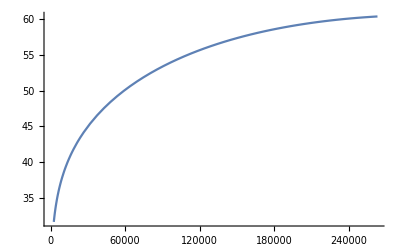

```mathematica
Plot[M1[x],{x,0, 2^(18)+1000}]
```

```mathematica
Err=ErrorListPlot[{DS1,DS2,DS3,DS4,DS5,DS6}];
```

```mathematica
BF = Plot[{M1[x],M2[x],M3[x],M4[x],M5[x],M6[x]},{x,0,2^(18)+1000}, PlotLegends->{"1 Thread","4 Threads" , "16 Threads", "64 Threads", "256 Threads", "1024 Threads"}, PlotRange->{{0,2^(18)+1000},{0,80}}];
```

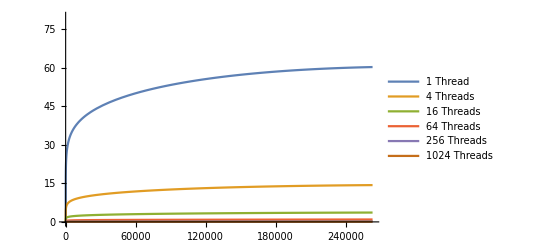

```mathematica
BF
```

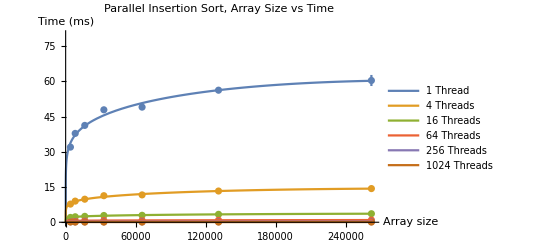

```mathematica
Show[Err,BF,AxesLabel-> {"Array size", "Time (ms)"},PlotRange->{{0,2^(18)+1000},{0,80}}, PlotLabel-> "Parallel Insertion Sort, Array Size vs Time"]
```

```mathematica
Coeffs={{1,a/.M1["BestFitParameters"][[1]]},{4, a/.M2["BestFitParameters"][[1]]}, {16,a/.M3["BestFitParameters"][[1]]}, {64,a/.M4["BestFitParameters"][[1]]}, {256,a/.M5["BestFitParameters"][[1]]}, {1024,a/.M6["BestFitParameters"][[1]]}}
```

{{1,-0.0000471632},{4,-9.82687×10^-6},{16,-1.74605×10^-6},{64,-4.535×10^-8},{256,3.2556×10^-7},{1024,4.32289×10^-7}}

```mathematica
Lm=LinearModelFit[Coeffs,x,x]
```

FittedModel[-0.0000135026+1.68441×10^-8 x]

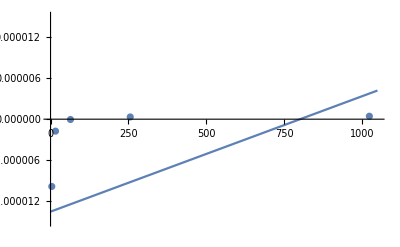

```mathematica
Show[{ListPlot[Coeffs],Plot[Lm[x],{x,1,1050}]}, PlotRange->{{0,1050},{-.000015,.000015}}]
```

```mathematica
Coeffs
```

{{1,-6.0004×10^-10},{4,-1.36741×10^-10},{16,-3.19424×10^-11},{64,-6.73151×10^-12},{256,-5.99511×10^-13},{1024,9.81246×10^-13}}

```mathematica
Lm["RSquared"]
```

0.135666

```mathematica
tab = {DA1, DA2, DA3, DA4, DA5,DA6}
```

{{{4096,32.0236},{8192,37.8644},{16384,41.2728},{32768,47.9297},{65536,49.0645},{131072,56.29},{262144,60.4217}},{{4096,7.73841},{8192,9.00864},{16384,9.8242},{32768,11.3176},{65536,11.6584},{131072,13.3122},{262144,14.3511}},{{4096,2.05321},{8192,2.33332},{16384,2.51658},{32768,2.88157},{65536,2.9597},{131072,3.37577},{262144,3.6383}},{{4096,0.563709},{8192,0.646294},{16384,0.670705},{32768,0.751317},{65536,0.764765},{131072,0.870066},{262144,0.935681}},{{4096,0.200529},{8192,0.190621},{16384,0.202769},{32768,0.212709},{65536,0.209761},{131072,0.235579},{262144,0.249855}},{{4096,0.106572},{8192,0.0809857},{16384,0.0693056},{32768,0.0659187},{65536,0.0688299},{131072,0.0738711},{262144,0.0763177}}}

```mathematica
TableForm[tab]
```

4096
32.0236 | 8192
37.8644 | 16384
41.2728 | 32768
47.9297 | 65536
49.0645 | 131072
56.29 | 262144
60.4217
4096
7.73841 | 8192
9.00864 | 16384
9.8242 | 32768
11.3176 | 65536
11.6584 | 131072
13.3122 | 262144
14.3511
4096
2.05321 | 8192
2.33332 | 16384
2.51658 | 32768
2.88157 | 65536
2.9597 | 131072
3.37577 | 262144
3.6383
4096
0.563709 | 8192
0.646294 | 16384
0.670705 | 32768
0.751317 | 65536
0.764765 | 131072
0.870066 | 262144
0.935681
4096
0.200529 | 8192
0.190621 | 16384
0.202769 | 32768
0.212709 | 65536
0.209761 | 131072
0.235579 | 262144
0.249855
4096
0.106572 | 8192
0.0809857 | 16384
0.0693056 | 32768
0.0659187 | 65536
0.0688299 | 131072
0.0738711 | 262144
0.0763177

```mathematica
D[a x Log[x] +b x + c Log[x],{x,2}]
```

-c/x^2+a/x